\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Descriptive Statistics

The purpose of this chapter is to introduce the reader to some methods used by statisticians and those who apply statistical methods to quickly describe data or to convey the essential information contained in a set of data.  The result of applying descriptive methods such as these is communication of the information in the data to a consumer of the information.  The information consumers may a professional or layman, who may need the information to make a crucial decision or may have a mild interest in the information contained in the data.  The consumer of the information may often be the data analyst who is only attempting to explore the data.

It is always important to be cognizant of the interest and skills of the information consumer, but the methods described in this chapter are straight forward and will most often be useful for quickly conveying a great deal of information to information consumers of varied backgrounds.  Data description, exploration and summary using methods like these is almost always the first step in analyzing a data set and is often sufficient to communicate the essence of the information in the data to its eventual consumer.

Since one of the purposes of statistics is to summarize, some of the actual detail of the data set must be sacrificed in order to achieve our goal of summarization and quick communication.  We will describe how an extensive list of numerical values may be summarized to reveal essential characteristics of the data in a table, a frequency distribution.  Although specific values are not available in a frequency distribution, if carefully constructed this tabular arrangement of the data conveys a good deal on the information avalable in a complete listing of the data, and with a little effort this information may be consumed by a reader with little or no statistical training.  The effort required to extract information from a tabular summary can be substantially reduced by providing a visual summary in the form of a graph.  Here again, we have traded detail for speed of communication.  Each time we make such a trade, we increase the likelihood that the consumer will capture the essence of the data.  A fairly radical summarization of data is a statistic, e.g. mean, median, range.  Presenting  and consuming information in this abbrieviated form must be done with extreme care since a very small segment of the data can have a very large impact on the result that the statistic reports.  When we examine some relatively recent exploratory techniques, it will be surprising how much detail can be retained in some of the simple visual methods of data description, e.g. stem-and-leaf diagrams, box and whisker plots.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Section. Data

Generally, we organize data in lists or arrays.  When data from more than one list are correlated the data are usually recorded in a data matrix, i.e. a list of lists.  Below is a data array listing the surface roughness of 15 ceramic substrates used in the manufacturing of computer chips.  Note that this is a rather small data array and therefore will be a convenient example to use to illustrate some of the notions in this chapter.

```mathematica
roughness={14.8, 14.4, 11.5, 10.0, 9.0, 9.1, 12.5, 8.6, 8.0, 9.3, 9.4, 10.1, 9.1, 7.6, 7.3};
```

An ordered data array is an arrangement of the data in ascending or descending order.  For example, for the data array of surface roughness of the 15 substrates referred to above, the ordered data array in ascending order would be: (7.3, 7.4, 8.0, 8.6, 9.0, 9.1, 9.1, 9.3, 9.4, 10.0, 10.1, 11.5, 12.5, 14.4, 14.8) , or

```mathematica
orderedRoughness=Sort[roughness]
```

{7.3,7.6,8.,8.6,9.,9.1,9.1,9.3,9.4,10.,10.1,11.5,12.5,14.4,14.8}

From the ordered array, we get a quick impression about some of the values in the array, like the minimum and maximum values and values that lie toward the center of the data.  But even with a small array that has been ordered, we are apt to miss some characteristics of the data.  You can imagine how large amounts of data exacerbate this problem.  tPrices is a moderately sized array of 60 closing prices for a share of AT&T common stock recorded toward the end of each of month starting in August, 1993.  Information like this may be obtained from a variety of web sites, e.g.  http://research.web.aol.com/.  We can observe that the prices are between $30 and $70, but there are characteristics of these data that are not evident from the data array or the ordered array.

```mathematica
tPrices={47.1562,44.1562,43.125,40.9687,39.375,42.5625,39.375,38.4375,38.4375,40.9687,40.7812,40.9687,40.9687,40.5,41.25,36.8437,37.6875,37.4062,38.7187,38.8125,38.0625,38.0625,39.75,39.5625,42.4687,49.3125,48,49.4062,48.5625,50.1562,47.7187,45.8437,45.9375,46.7812,46.5,39.1875,39.375,39.1875,35,39.25,43.625,39.375,39.875,34.75,33.5,36.75,35,36.8125,39,44.25,48.875,55.875,61.25,62.625,61,65.75,60.1875,60.875,57.125,60.625};
```

```mathematica
Sort[tPrices]
```

{33.5,34.75,35,35,36.75,36.8125,36.8437,37.4062,37.6875,38.0625,38.0625,38.4375,38.4375,38.7187,38.8125,39,39.1875,39.1875,39.25,39.375,39.375,39.375,39.375,39.5625,39.75,39.875,40.5,40.7812,40.9687,40.9687,40.9687,40.9687,41.25,42.4687,42.5625,43.125,43.625,44.1562,44.25,45.8437,45.9375,46.5,46.7812,47.1562,47.7187,48,48.5625,48.875,49.3125,49.4062,50.1562,55.875,57.125,60.1875,60.625,60.875,61,61.25,62.625,65.75}

A natural solution to our inability to store and organize this much information in our short-term memories is to create categories of possible values and tabulate the data.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Section. Tabular Summaries (Frequency Distributions)

A frequency distribution is a tabular arrangement of the data by categories called classes.  Note that some of the original information contained in the data array is lost when the data is grouped into categories.  Each class is defined by its lower and upper class limits.  Suppose we decide to form the following five categories for describing the roughness data, {{6.0, 7.9}, {8.0, 9.9}, {10.0, 11.9}, {12.0, 13.9}, and {14.0, 15.9}}.  8.0 is called the lower class limit of the 2nd class and 9.9 is the upper class limit of that class.  The resulting class intervals divide the data into mutually exclusive categories, i.e., the class intervals are said to partition the set of possible values of surface roughness.

The upper real class limit of a class is a point between the upper class limit of the class and the lower class limit of the next class.  It is usually chosen to be the mid-point between the upper class limit of a class and the lower class limit of the next class.  By letting the real class limits define the categories, the categories are viewed as being overlapping.  Adjacent categories are made tangent to one another by letting the upper real class limit of a class be the lower real class limit of the next class.  The real class limits are also called class boundaries or continuous class limits.  The width of a class is the difference between the continuous upper class limit and  the continuous lower class limit of that class.

Note:  It is important to realize that certain statistical terms like significant, correlated, expected value, accept, etc. have very specific meanings when used in a statistical context.  Frequently that meaning does not correspond to popular English usage.  If this is not born in mind it can lead to serious misconceptions.  Many authors will use these terms loosely, thereby misleading their readers.  The word real in the expression real class limit refers to the mathematical notion of a real number.  It does not mean actual.  In fact, to the degree of accuracy used to record data in our array, the real class limits are impossible observations.

The class midpoint is the midpoint of the class interval.  The table below illustrates these terms for the roughness data.

Class
	Limits |                    Real
	Class
	Limits | 
	Class
	Midpoint | 
	Class
	Width | 
	
	Frequency | 
	Relative
	Frequency | 
	Cumulative
	Frequency |                 Cumulative
	Relative
	Frequency
6.0-7.9 | 5.95-7.95 | 6.95 | 2 | 2 | 0.13  | 2 | 0.13 
8.0-9.9 |  7.95-9.95 | 8.95 | 2 | 7 | 0.47 | 9 | 0.60
10.0-11.9 |  9.95-11.95 | 10.95 | 2 | 3 | 0.20 | 12 | 0.80
12.0-13.9 | 11.95-13.95 | 12.95 | 2 | 1 | 0.07 | 13 | 0.87
14.0-15.9 | 13.95-15.95 | 14.95 | 2 | 2 | 0.13 | 15 | 1.00
  |   |   |   | 15 | 1.0 |   |

The relative frequency of a class is the class frequency divided by the total number of observations in the data, i.e the proportion of observations observed in that class.  The cumulative frequency of a class is the number of observations in that class and all preceding classes, or the number of observations falling at or below the upper class limit of that class.  The relative cumulative frequency is the cumulative frequency of a class divided by the total frequency, or the proportion of observations below the continuous class limit of that class.

It is clear that the information in the columns for class limits, real class limits, and class midpoints is redundant, as is the information in the last four columns.  Consequently, we usually represent the data with a subset of these columns.  For example,

Class
	Boundries | 
	
	Frequency | 
	Relative
	Frequency
5.95-7.95 | 2 | 0.13 
 7.95-9.95 | 7 | 0.47
 9.95-11.95 | 3 | 0.20
11.95-13.95 | 1 | 0.07
13.95-15.95 | 2 | 0.13
  | 15 | 1.0

Section.Subsection.Subsubsection.  Frequency Distribution Example with tPrices

The last section of this chapter contains some functions for obtaining the frequency distribution.  We use them to explore the data array, tPrices.  Noticing that the minimum and maximum of tPrices are 33.5 and 65.75, respectively, suppose we partition the range of tPrices values into eight classes of equal width 5, beginning with 29.95,

```mathematica
{Min[tPrices], Max[tPrices]}
```

{33.5,65.75}

```mathematica
tPricesClassBoundriesByClass = Table[{x,x+5}, {x, 24.95, 79.95, 5}]
```

{{24.95,29.95},{29.95,34.95},{34.95,39.95},{39.95,44.95},{44.95,49.95},{49.95,54.95},{54.95,59.95},{59.95,64.95},{64.95,69.95},{69.95,74.95},{74.95,79.95},{79.95,84.95}}

```mathematica
{tPricesClassBoundriesByClass,tPricesClassFrequencies}//TableForm
```

24.95
29.95 | 29.95
34.95 | 34.95
39.95 | 39.95
44.95 | 44.95
49.95 | 49.95
54.95 | 54.95
59.95 | 59.95
64.95 | 64.95
69.95 | 69.95
74.95 | 74.95
79.95 | 79.95
84.95
0 | 2 | 24 | 13 | 11 | 1 | 2 | 6 | 1 | 0 |  |

Now we notice a feature of the data that was not immediately apparent from the listing of the data array.  The data are concentrated in the first half of the distribution.  The distribution of tPrices is said to be positively skewed.  More precisely, these data are positively skewed because the mean exceeds the median of these data.  Shortly, we will encounter the mean and median as descriptive measures or statistics.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

Section.Subsection.  Histograms

A histogram is set of rectangles corresponding to the classes in a frequency distribution such that the bases of the rectangles are determined by the real class limits and the areas of the rectangles are proportional to the class frequencies.

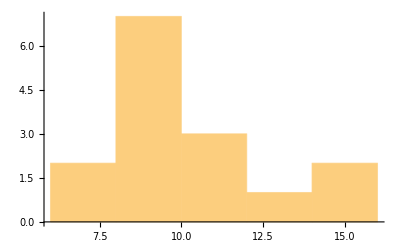

```mathematica
Histogram[{7.3,7.6,8.,8.6,9.,9.1,9.1,9.3,9.4,10.,10.1,11.5,12.5,14.4,14.8}]
```

or

```mathematica
Histogram[roughness]
```

-Graphics-

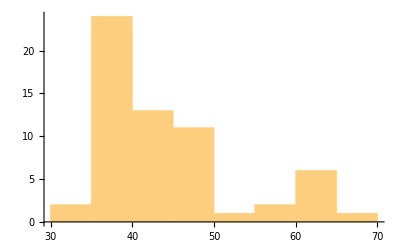

```mathematica
Histogram[tPrices]
```

Number of bins, 10

```mathematica
Histogram[tPrices,10]
```

-Graphics-

Bin width, 5.

```mathematica
Histogram[tPrices,{5}]
```

-Graphics-

Number of bins, 15.

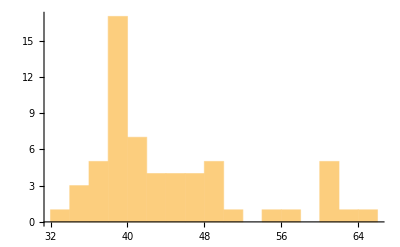

```mathematica
Histogram[tPrices,15]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

Section.Subsection.  Frequency Polygons and Relative Frequency Polygons

A (relative) frequency polygon is a graph of the class relative frequencies against the class midpoints.  Notice to make this graph appear to be a polygon, it is necessary to define two more classes, one below the first class and one above the last class, both of which are empty, i.e. with frequency zero.

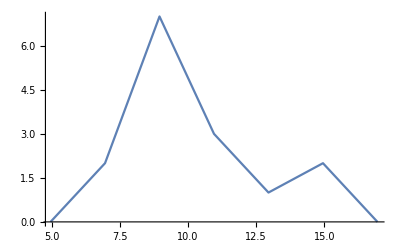

```mathematica
ListLinePlot[{{4.95,0},{6.95,2},{8.95,7},{10.95,3},{12.95,1},{14.95,2},{16.95,0}}]
```

The concept of areas under curves representing relative frequencies and probabilities is an important notion in the study of Probability and Statistics.  You will notice that if you connect the midpoints of the tops of the rectangles making up the histogram, you will produce the polygon and that these two figures have the same area.  This fact is easily proven by noticing that the portions of both figures that are not common to both are a sequence of congruent triangles.

The positive skew in the tPrices data is readily apparent in the relative frequency polygon.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

Section.Subsection. Relative Cumulative Frequency Graphs or Empirical cdf's

A relative cumulative frequency graph is a plot of class relative cumulative frequencies against upper real class limits and thus is a graph depicting the proportion of observations at or below any value.

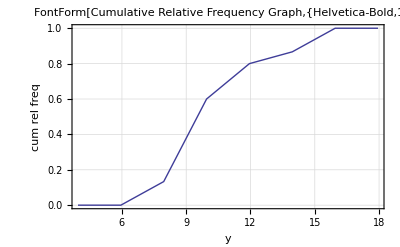

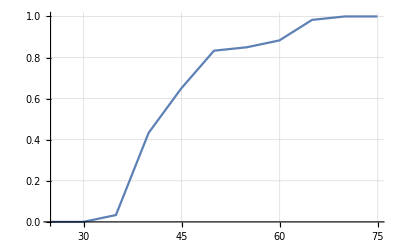

```mathematica
DiscretePlot[CDF[EmpiricalDistribution[tPrices],y],{y,24.95,74.95,5},Joined->True,Filling->None,GridLines->Automatic]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Section. Measures Summarizing Data (Statistics)

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

Section.Subsection.  Measures of Location

The kth percentile is a point below which k percent of the values of the distribution fall.  The percentile rank of a score is the proportion of scores that fall below that point.  The first quartile is the 25th percentile. The second quartile is the 50th percentile. The third quartile is the 75th percentile. The first decile is the 10th percentile, etc.  For example,

```mathematica
Quantile[tPrices, 0.50]
```

40.9687

```mathematica
{Quantile[tPrices, 0.25],Quantile[tPrices, 0.50],Quantile[tPrices, 0.75]}
```

{38.8125,40.9687,47.7187}

```mathematica
Quartiles[tPrices]
```

{38.9063,40.9687,47.8594}

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

Section.Subsection.Subsubsection.  Measures of Central Tendency

Measures of central tendency are statistics that attempt to describe the center of the distribution which may be thought of in a number of ways.  It is important to understand the distinction among these measures because often they are the only information reported about data, especially in advertising and the media in general.  The ability to describe data using one measure is powerful in as much as the information (or misinformation) is conveyed in a matter of a few seconds.  Thus we must take special care when reporting these statistics, as with all information, that we are accurately representing the data.  For example, the mean income for a very skewed distribution of incomes is considerably larger than the income of most individuals.  On the other hand, in a statistical audit, the median of the distribution of transaction errors tells you almost nothing about the total dollars in error regardless of the positive skew common in most distributions of this type.

The median is the 50th percentile.  The mode is the score that occurs most frequently.  The modal class is the class with the greatest frequency.  The mean of a distribution is the average of the scores in the distribution and is usually denoted by placing a bar above the variable in question, e.g. x̄, or ȳ, or OverBar[tPrice].  The mean is the center of gravity of the distribution.  When discussing set theory, which we will do briefly in another chapter, we will need to denote the complement of a set.  Some authors would denote the complement of a set A by Ā , or ∼A.  We will avoid this possible confusion by using A' or A^c.  The ∼ symbol is used in Probability and Statistics to describe the shape or form of a distribution as in Y∼Normal.

ȳ=(1/n∑)_(i=1)^n y_i

```mathematica
{Mean[tPrices],Median[tPrices],Commonest[tPrices]}
```

{44.2292,40.9687,{40.9687,39.375}}

Note that the mean of tPrices exceeds the median and therefore the distribution is postitively skewed.  And apparently there are two modes.  Each has relative frequency 4/60or 0.27.

The mean, median and mode are called measures of central tendency. Each of these measures represents an attempt to describe the location of the center of the distribution.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

Section.Subsection.  Measures of Dispersion

The range is the difference between the largest and smallest score in a distribution.  The interquartile range (IQR) is the difference between the 75th percentile and the 25th percentile.  The range for the roughness distribuiton is 7.5.

```mathematica
{Min[roughness],Max[roughness]}
```

{7.3,14.8}

```mathematica
range=Max[roughness]-Min[roughness]
```

7.5

```mathematica
Quartiles[roughness]
```

{8.7,9.3,11.15}

```mathematica
InterquartileRange[roughness]
```

2.45

The variance, s^2, of a set of data is defined as follows:

s^2=∑_(i=1)^n (y_i-ȳ)^2/(n-1)

The variance represents the average squared deviation about the mean. The standard deviation, s, is the square root of the variance.

```mathematica
{Variance[roughness],StandardDeviation[roughness]}
```

{5.23981,2.28906}

In finance, the risk of an investment or portfolio is its standard deviation.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

Section.Subsection.Subsubsection.  Chebychev's Rule

Chebychev's Rule states that at least 1-1/k^2 of any distribution will fall within k standard deviations of the mean.  For example, at least 3/4 of a distribution is between x̄-2 s and x̄+2 s while at least 8/9of any distribution will be in {x̄-3 s, x̄+3 s}.  For the stock prices in tPrices, Chebychev guarantees us that at least

```mathematica
1-1/(2.5)^2
```

0.84

of the 60 prices, i.e. at least 51 prices are in the interval

```mathematica
{Mean[tPrices]-2.5 StandardDeviation[tPrices],Mean[tPrices]+2.5 StandardDeviation[tPrices]}
```

{24.084,64.3743}

In fact, 59 of the 60 prices are within this interval.  We note that since Chebychev works for any distribution that it must be naturally conservative.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

Section.Subsection.Subsubsection.  The Empirical Rule

If the distribution is approximately bell shaped, the empirical rule says that approximately 68% of the distribution will fall between x̄-1 s and x̄+1 s, while approximately 95% of the distribution will fall between bar x̄-2 s and x̄+2 s, and more than 99% will be in the interval {x̄-3 s and x̄+3 s}.

For the tPrices data, these three intervals are

```mathematica
Table[{Mean[tPrices]-k StandardDeviation[tPrices],Mean[tPrices]+k StandardDeviation[tPrices]},{k,1,3}]
```

{{36.1711,52.2872},{28.113,60.3453},{20.055,68.4033}}

For the tPrices data, the number of prices falling to the left, within, and to the right of these three intervals is

{{4,47,9},{0,54,6},{0,60,0}}

or, in terms of proportions

{{0.0666667,0.783333,0.15},{0.,0.9,0.1},{0.,1.,0.}}

Here, 0.78 is considerably more than 68% and 0.90 is appreciably less than 95%.  Our empirical rule is not applicable here because of the positive skew noticed earlier in the frequency distribution and the relative frequency polygon for tPrices.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

Section.Subsection.Subsubsection.  An Example of the Mean and Standard Deviation in Finance, Expected Relative Return and Risk

Suppose we purchased some shares of common stock at $95 and one month later noticed that its value had risen to $100, a gain of $5 which we call the return for that month.  In relative terms, that is relative to the value of the security at the beginning of the month, we have 5/95=0.0526 which may be thought of as 5.26% monthly interest.  Now suppose that after two months, the price is $105, another $5 monthly return, but only 5% relative to the value of stock at the beginning of the second month.  Clearly,  monthly return and relative monthly return may be negative.  If during the third month, the price has dropped to $95, we have $10 loss, or a relative return of -10/105=-0.0952.  The functions below reiterate this example.

When studying finance, expected monthly relative return is the average of these monthly relative returns, and the standard deviation of the monthly relative returns is called risk.

A more realistic example is tPrices.

The ratio of the standard deviation to the mean is called the coeffficient of variation, here

```mathematica
coeffOfVar[x_]:=StandardDeviation[x]/Mean[x]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Section. Exploratory Techniques

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

Section.Subsection.  Stem-and-Leaf Diagrams

A stem-and-leaf diagram is one method used to generate initial information about a set of data.  The result is a figure, very similar to a histogram, but one that retains all of the detail of the original array of observations.  We will introduce the essential elements of a stem-and-leaf diagram.  For a more detailed description see Tukey (1977).

The stem is vertically ordered list of the numbers, frequently the range of possible values of the observations carried out to one place less than the actual observations.  For example, using the 15 surface roughnesses listed earlier, the stem consists of the integers between 7 and 14.

07|
08|
09|
10|
11|
12|
13|
14|

The leaves are usually comprised of the last significant digit of each observation assuming that each observation contains the same number of decimal places.  In the surface roughness example, the leaves are composed of the tenths digits in the observations.  The leaves are listed horizontally attached to their appropriate stem.  For example:

07| | 6 | 3 |   |   |  
08| | 6 | 0 |   |   |  
09| | 0 | 1 | 3 | 4 | 1
10| | 0 | 1 |   |   |  
11| | 5 |   |   |   |  
12| | 5 |   |   |   |  
13| |   |   |   |   |  
14| | 8 | 4 |   |   |

If the leaves are ordered, the result is an ordered stem-and-leaf diagram.

07| | 3 | 6 |   |   |  
08| | 0 | 6 |   |   |  
09| | 0 | 1 | 1 | 3 | 4
10| | 0 | 1 |   |   |  
11| | 5 |   |   |   |  
12| | 5 |   |   |   |  
13| |   |   |   |   |  
14| | 4 | 8 |   |   |

This diagram provides a visual description of the information contained in the data while retaining all of the detail of the original data array.  Also measures such as the median, mode, percentiles and ranges are readily available from the diagram.

If observations from two different sources, say different treatments, or different tools, are diagramed one on each side of the stem, the result is a back-to-back stem-and-leaf diagram which is useful for comparing two data sets.

|   |   | B |   | stem |   | A |   |   |  
  | 4 | 2 | 1 | 1 | |07| | 3 | 6 |   |   |  
  |   |   | 2 | 0 | |08| | 0 | 6 |   |   |  
  |   |   |   |   | |09| | 0 | 1 | 1 | 3 | 4
  | 5 | 4 | 3 | 3 | |10| | 0 | 1 |   |   |  
  |   | 1 | 1 | 0 | |11| | 5 |   |   |   |  
  |   |   |   | 0 | |12| | 5 |   |   |   |  
  |   |   | 6 | 2 | |13| |   |   |   |   |  
  |   | 3 | 2 | 1 | |14| | 4 | 8 |   |   |

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

Section.Subsection.  Box and Whisker Plots

Box and whisker plots are graphical methods for describing data arrays, and when more than one array is of interest, for making comparisons among them.  The horizontal axis indexes the arrays of  data and  the vertical axis corresponds to the range of measurements in the data, a box is constructed for each array.  The widths of the boxes are arbitrary, but uniform.  The bottom and top of the boxes correspond to the 25th and 75th percentiles of each array, respectively. A horizontal line is drawn through the box at the median and whiskers protruding vertically from the box are extended to the minimum and maximum values in each subset.  Since the whiskers occupy little space, space is available to identify extremely large and small observations.

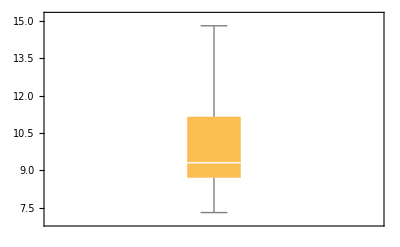

```mathematica
BoxWhiskerChart[roughness]
```

The boxplot below compares the monthly relative returns for six stocks.

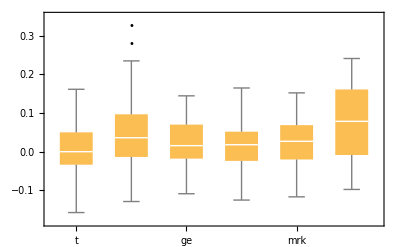

```mathematica
BoxWhiskerChart[{tRelativeReturns,msftRelativeReturns,geRelativeReturns,disRelativeReturns,mrkRelativeReturns,luRelativeReturns},"Outliers",ChartLabels->{"t","msft","ge","dis","mrk","lu"}]
```

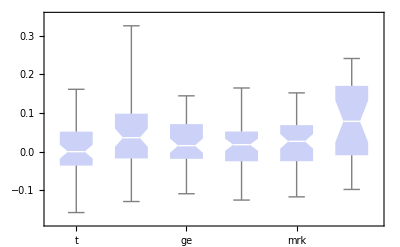

```mathematica
BoxWhiskerChart[{tRelativeReturns,msftRelativeReturns,geRelativeReturns,disRelativeReturns,mrkRelativeReturns,luRelativeReturns},"Notched",ChartLabels->{"t","msft","ge","dis","mrk","lu"}]
```